-Graphics3D-

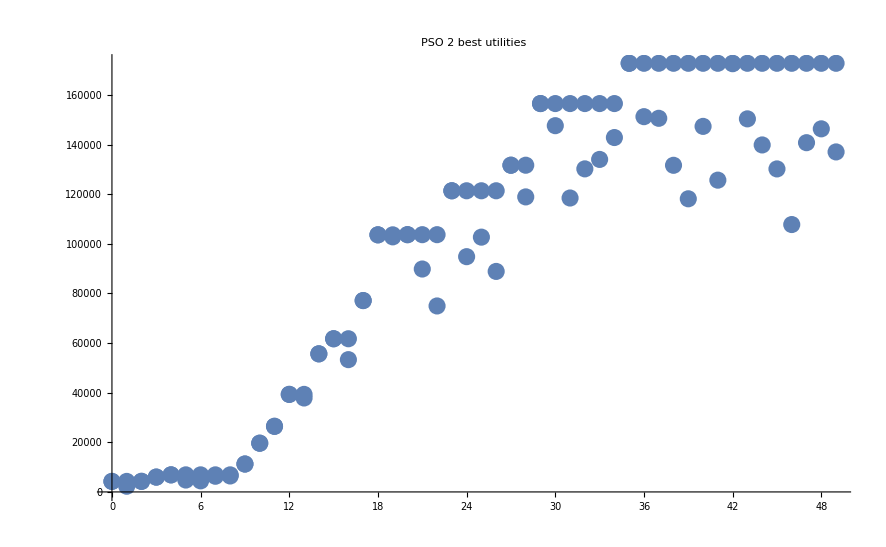

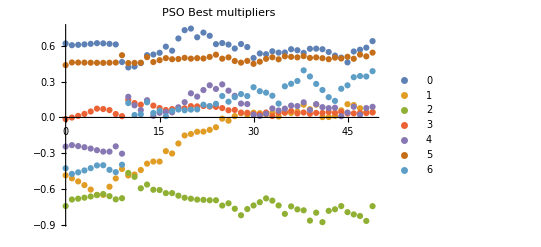

-Graphics3D-

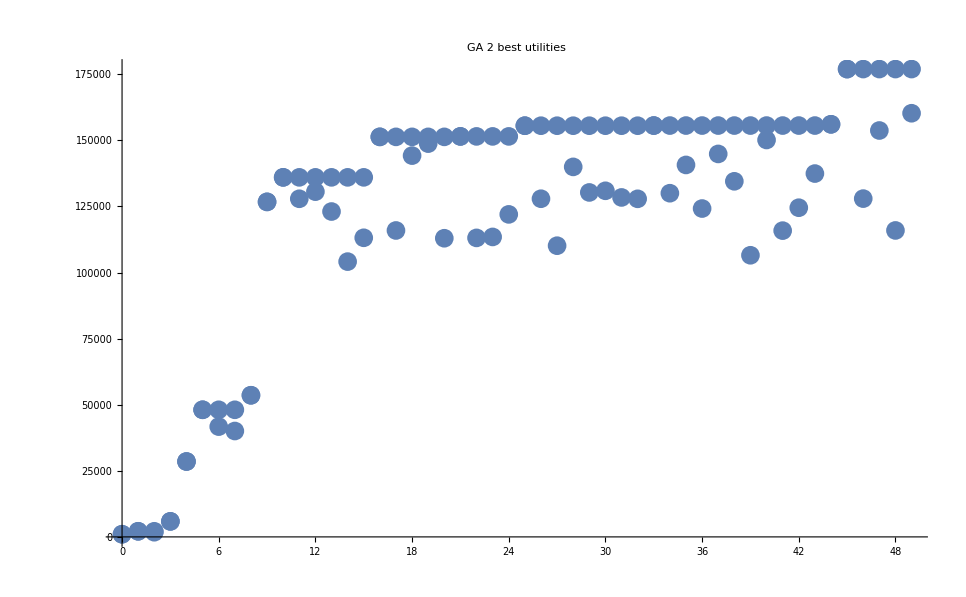

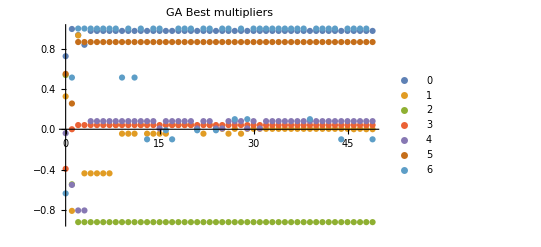

{Null,Null}

```mathematica
algorithms = {"PSO", "GA"};
COUNTOFPARAMS = 7;

Table[
ListPointPlot3D[Import[FileNameJoin[{NotebookDirectory[], StringJoin[i,"_allUtilities.log"]}], "Table"], PlotRange-> All, PlotLabel-> StringJoin[i," all utilities"]] // Print
;

ListPlot[Import[FileNameJoin[{NotebookDirectory[], StringJoin[i,"_twoBestUtilities.log"]}], "Table"], PlotRange-> All, PlotLabel -> StringJoin[i," 2 best utilities"]]  // Print

;

in = Import[FileNameJoin[{NotebookDirectory[], StringJoin[i,"_bestMultipliers.log"]}], "Table", FieldSeparators -> { ",", " "}];
ListPlot[Partition[in, Length[in]/COUNTOFPARAMS],PlotLegends->Table[i-1, {i,COUNTOFPARAMS}], PlotRange-> All,PlotLabel->StringJoin[i," Best multipliers"]] // Print
, {i, algorithms}]
```

```mathematica
algorithms = {"PSO_test0", "PSO_test1", "PSO_test2", "PSO_test3", "PSO_test4", "GA_test0", "GA_test1","GA_test2", "GA_test3", "GA_test4"};
COUNTOFPARAMS = 7;

Table[
ListPointPlot3D[Import[FileNameJoin[{NotebookDirectory[], StringJoin[i,"_allUtilities.log"]}], "Table"], PlotRange-> All, PlotLabel-> StringJoin[i," all utilities"]] // Print
;

ListPlot[Import[FileNameJoin[{NotebookDirectory[], StringJoin[i,"_twoBestUtilities.log"]}], "Table"], PlotRange-> All, PlotLabel -> StringJoin[i," 2 best utilities"]]  // Print

;

in = Import[FileNameJoin[{NotebookDirectory[], StringJoin[i,"_bestMultipliers.log"]}], "Table", FieldSeparators -> { ",", " "}];
ListPlot[Partition[in, Length[in]/COUNTOFPARAMS],PlotLegends->Table[i-1, {i,COUNTOFPARAMS}], PlotRange-> All,PlotLabel->StringJoin[i," Best multipliers"]] // Print
, {i, algorithms}]
```